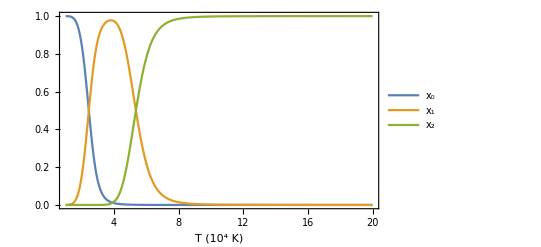

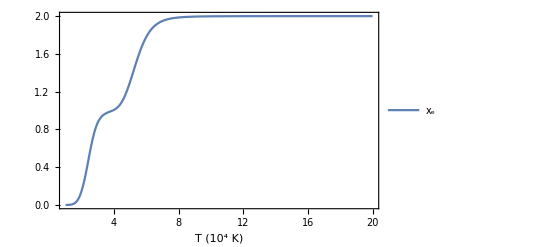

{T→24360.2}

{T→53494.7}

```mathematica
(* Define constants *)
mHe =4*1.67262*10^{-24};
me=9.10938*10^{-28};
h=6.62608*10^{-27};
k=1.38066*10^{-16};
eVtoerg=1.60218*10^{-12};
chi0=24.6*eVtoerg;
chi1=54.4*eVtoerg;
(* Choose rho = 10^-6 *)
rho=10^{-6};

(* Define functions to solve *)
f1[x1_,x2_,T_]:=(x1^2+2*x1*x2)/(1-x1-x2)-mHe/rho*(2π*me*k*T/h^2)^{3/2}*Exp[-chi0/(k*T)] ;
f2[x1_,x2_,T_]:=(2*x2^2+x1*x2)/x1-mHe/rho*(2π*me*k*T/h^2)^{3/2}*Exp[-chi1/(k*T)];
Soln[T_]:=Quiet[Solve[f1[x1,x2,T]==0&&f2[x1,x2,T]==0&&x1>0&&x2>0,{x1,x2}]];

(* Define output functions for each x *)
x1[T_]:=x1/.Soln[T];
x2[T_]:=x2/.Soln[T];
x0[T_]:=1-x1[T]-x2[T];
xe[T_]:=x1[T]+2*x2[T];

(* Make plots *)
Plot[{x0[T*10^4],x1[T*10^4],x2[T*10^4]},{T,1, 20},FrameLabel->HoldForm[T(Superscript[10,4]K)],Frame->True,PlotLegends->LineLegend[Automatic,{Subscript[x,0],Subscript[x,1],Subscript[x,2]}]]
Plot[{xe[T*10^4]},{T,1,20},FrameLabel->HoldForm[T(Superscript[10,4]K)],Frame->True,PlotLegends->LineLegend[{Subscript[x,e]}]]

(* Find transition temperatures *)
T1=Quiet[FindRoot[Abs[x1[T]-x0[T]],{T,2.5*10^4}]]
T2=Quiet[FindRoot[Abs[x2[T]-x1[T]],{T,5.5*10^4}]]
```